## 习题4

#### 4 - 8

```mathematica
Reduce[Log[p1/p2]==ΔH/R(1/T1-1/T2)/.{T1->(273.15+99),T2->(273.15+101),p1->13.6*1*10^3*9.8*733.7*10^-3,p2->13.6*1*10^3*9.8*788.0*10^-3,R->8.314}]
```

ΔH==-41326.5

故汽化热为41326.5 J/mol.

#### 4 - 10

```mathematica
Reduce[ΔH/R==-7527/.R->8.314]
```

ΔH==-62579.5

故升华热为62579.5 J/mol.

#### 4 - 12

```mathematica
Reduce[Log[p1/p2]==-ΔH/R(1/T1-1/T2)/.{p1->13.6*1*10^3*9.8*760*10^-3,p2->13.6*1*10^3*9.8*770*10^-3,T1->373.15,ΔH->2.26*10^6/1000*18,R->8.314}]
```

T2==373.522

```mathematica
373.522-273.15
```

100.372

故水的沸点为100(.372)^o C.

#### 4-15

```mathematica
Solve[{Log[p]==23.3-3254/T,Log[p]==19.49-3063/T},{p,T}]
```

{{p→8.49505×10^-19,T→50.1312}}

故三相点压强为8.49505 mmHg, 温度为 50.1312 K.

```mathematica
3063*8.314
```

25465.8

```mathematica
3754*8.314
```

31210.8

```mathematica
%-%%
```

5744.97

故汽化热为 25465.8 J/mol, 升华热为31210.8 J/mol, 熔化热为 5744.97 J/mol.

#### (5).

(a).

dP/dT== -L_m/TΔV_m

考虑到固体与液体的体积随温度变化量较小，故认为ΔV_m 与T无关。

故 p==-L_m/ΔV_mLog[T]+p_0

```mathematica
Reduce[ΔVm==0.018/Subscript[ρ, 水]-0.018/Subscript[ρ, 冰]/.{Subscript[ρ, 水]->1*10^3,Subscript[ρ, 冰]->0.9*10^3}]
```

ΔVm==-2.×10^-6

考虑到三相点 {T -> 273.16, p -> 610.75} 在该线上，

```mathematica
Reduce[p==Subscript[L, m]/Subscript[ΔV, m] Log[T]+Subscript[P, 0]/.{T->273.16,p->610.75,Subscript[L, m]->6030,Subscript[ΔV, m]->-2*10^-6}]
```

P_0==1.69143×10^10

```mathematica
Subscript[L, m]/Subscript[ΔV, m] Log[T]+Subscript[P, 0]/.{Subscript[L, m]->6030,Subscript[ΔV, m]->-2*10^-6,Subscript[P, 0]-> 1.69*10^10}
```

1.69×10^10-3015000000 Log[T]

故p=-3.015*10^9 Log[T]+1.69*10^10(Pa).

(b).

这是由于冰的密度比水小，使得系数小于0。而这个的原因是水分子之间的氢键。

(c).

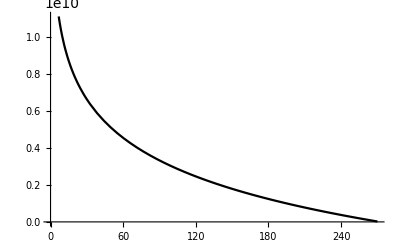

```mathematica
Plot[-3.015*10^9 Log[T]+1.69*10^10,{T,0,270},PlotStyle->Black]
```

#### (6).

Log[p_1/p_2]==-L_m/R(1/T_1-1/T_2)

调用第一次作业的数据于list.

```mathematica
GetV1[p_,T_]:=V/.Sort[NSolve[((p+a/V^2)*(V-b)==R*T/.{a->0.1378,b->3.183*10^-5,R->8.314}),V]];
list1=Flatten/@({#,Drop[GetV1@@#,{2}]}&/@(Drop[#,-1]&/@Flatten/@list));
```

L_m/TV_m=dP/dT≈ΔP/ΔT

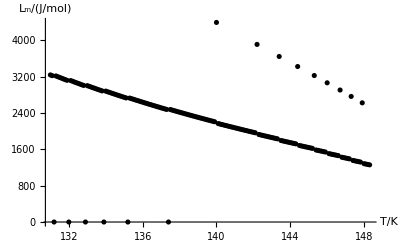

{{145.9,1541.64},{137.6,2464.91},{140.5,2125.85}}

```mathematica
list2=ReleaseHold[(HoldForm[{#[[k]][[2]],
(#[[k]][[2]](#[[k]][[4]]-#[[k]][[3]])(#[[k+1]][[1]]-#[[k]][[1]])/(#[[k+1]][[2]]-#[[k]][[2]]))}&
@list1]/.k->#&)/@Range[174]];
ListPlot[list2,AxesLabel->{"T/K","L_m/(J/mol)"},PlotStyle->Black]
RandomChoice[list2,3]
```

可以看出氧气液相变为气相的潜热随温度升高而降低，这是由于接近临界态，液相与气相“状态”越来越接近，从而转变所需潜热越来越少（图中有少数例外应该为元数据中含有的一些算法不好导致的错误数据）。由于为粗略估计，故图中的趋势并不为真实趋势。大致的潜热在 2000~3000 J/mol.

#### 4.3

(a).ΔG=n_1 μ_1+n_2 μ_2-n_1 g_1(T,p)-n_2 g_2(T,p)
	=RT(n_1 ln x_1+ n_2 ln x_2)
(b). dμ=V_m dP-S_m dT
dV_m =((∂μ)/(∂p))_T dp +S_m dT=0 (dp=0,dT=0)
Thus ΔV_m=0,ΔV=0
(c).S_m=-((∂μ)/(∂T))_p=-( ((∂g)/(∂T))_p+R ln x)
ΔS_m=-R ln x
ΔS=n_1 ΔS_(m,1)+n_2 ΔS_(m,2)
       =-R (n_1 ln x_1+n_2 ln x_2).
(d).ΔH=ΔG-Δ(TS)=RT(n_1 ln x_1+ n_2 ln x_2) - RT(n_1 ln x_1+ n_2 ln x_2)=0
(e).不变化。δQ=δW=0.

#### 4.4

(a). μ_1'=μ_1
g_1'=μ_1'=μ_1=g_1(T,p)+R T ln (1-x)
得证。
(b).蒸气的化学势又可表示为
μ_1' = RT ln p_1', p_1'表示蒸气压。
故 ((∂(R T ln p))/(∂ x))_T= ((∂(R T ln (1-x)))/(∂ x))_T,得 ((∂p)/(∂x))_T=-p/(1-x).

```mathematica
(*剩下部分见纸质*)
```

```mathematica
(*附元数据：*)
```

```mathematica
list={{{2530000,131},0.24273619969244464},{{2540000,131.1},0.5911133665667876},{{2550000,131.2},0.9313938186387531},{{2550000,131.29999999999998},1.176146331059499},{{2560000,131.39999999999998},0.8376143363784649},{{2570000,131.49999999999997},0.5069923805822327},{{2580000,131.59999999999997},0.18418518155704078},{{2590000,131.69999999999996},0.13090145896239846},{{2600000,131.79999999999995},0.43836067323354655},{{2610000,131.89999999999995},0.7382845449374145},{{2620000,131.99999999999994},1.0307641263534606},{{2620000,132.09999999999994},1.03251707250638},{{2630000,132.19999999999993},0.7411891820283927},{{2640000,132.29999999999993},0.4571325166070892},{{2650000,132.39999999999992},0.18025888723241223},{{2660000,132.49999999999991},0.08951892850200238},{{2670000,132.5999999999999},0.3522872020585055},{{2680000,132.6999999999999},0.6081312692913343},{{2690000,132.7999999999999},0.8571355455296725},{{2700000,132.8999999999999},1.099383540402414},{{2700000,132.9999999999999},0.9137873826311989},{{2710000,133.09999999999988},0.6720572860995162},{{2720000,133.19999999999987},0.4369240946671198},{{2730000,133.29999999999987},0.2083068025585817},{{2740000,133.39999999999986},0.013874746464352938},{{2750000,133.49999999999986},0.22969987265787495},{{2760000,133.59999999999985},0.4392470736256655},{{2770000,133.69999999999985},0.6425940374138008},{{2780000,133.79999999999984},0.8398176553855592},{{2790000,133.89999999999984},1.0309940348470263},{{2790000,133.99999999999983},0.9262825544064981},{{2800000,134.09999999999982},0.7349645969752601},{{2810000,134.19999999999982},0.5495478149932751},{{2820000,134.2999999999998},0.3699582550325431},{{2830000,134.3999999999998},0.19612269943172578},{{2840000,134.4999999999998},0.027968654667347437},{{2850000,134.5999999999998},0.13457566012039024},{{2860000,134.6999999999998},0.2915813243780576},{{2870000,134.79999999999978},0.4431187272348325},{{2880000,134.89999999999978},0.5892575784091605},{{2890000,134.99999999999977},0.7300669189407927},{{2900000,135.09999999999977},0.8656151317518379},{{2910000,135.19999999999976},0.9959699520477443},{{2910000,135.29999999999976},0.8874964948245179},{{2920000,135.39999999999975},0.7561938680737512},{{2930000,135.49999999999974},0.6299534079407749},{{2940000,135.59999999999974},0.5087091371115093},{{2950000,135.69999999999973},0.39239568590710405},{{2960000,135.79999999999973},0.28094828259600035},{{2970000,135.89999999999972},0.17430274387697864},{{2980000,135.99999999999972},0.07239546554228582},{{2990000,136.0999999999997},0.024836586781020742},{{3000000,136.1999999999997},0.11745588672965823},{{3010000,136.2999999999997},0.2055243561462703},{{3020000,136.3999999999997},0.2891033739761042},{{3030000,136.4999999999997},0.36825378493449534},{{3040000,136.59999999999968},0.44303590813251503},{{3050000,136.69999999999968},0.51350954557347},{{3060000,136.79999999999967},0.5797339904856926},{{3070000,136.89999999999966},0.6417680356171331},{{3080000,136.99999999999966},0.6996699813589657},{{3090000,137.09999999999965},0.7534976438146259},{{3100000,137.19999999999965},0.8033083627233282},{{3110000,137.29999999999964},0.8491590093199193},{{3120000,137.39999999999964},0.8911059940655832},{{3120000,137.49999999999963},0.8644266161536507},{{3130000,137.59999999999962},0.8202758000061294},{{3140000,137.69999999999962},0.7799167687771842},{{3150000,137.7999999999996},0.7432943125550082},{{3160000,137.8999999999996},0.7103536511931452},{{3170000,137.9999999999996},0.6810404269272112},{{3180000,138.0999999999996},0.6553006970934803},{{3190000,138.1999999999996},0.6330809269584279},{{3200000,138.29999999999959},0.6143279825409991},{{3210000,138.39999999999958},0.5989891235985851},{{3220000,138.49999999999957},0.5870119965893537},{{3230000,138.59999999999957},0.5783446277873736},{{3240000,138.69999999999956},0.5729354163850076},{{3250000,138.79999999999956},0.5707331276898913},{{3260000,138.89999999999955},0.571686886385578},{{3270000,138.99999999999955},0.5757461698121915},{{3280000,139.09999999999954},0.582860801339848},{{3290000,139.19999999999953},0.5929809437420772},{{3300000,139.29999999999953},0.606057092665651},{{3310000,139.39999999999952},0.622040070093135},{{3320000,139.49999999999952},0.6408810178672866},{{3330000,139.5999999999995},0.6625313912736601},{{3340000,139.6999999999995},0.6869429525941086},{{3350000,139.7999999999995},0.7140677647512348},{{3360000,139.8999999999995},0.7438581849492039},{{3370000,139.9999999999995},0.7762668583345658},{{3390000,140.09999999999948},0.7428276856589946},{{3400000,140.19999999999948},0.6967314656012604},{{3410000,140.29999999999947},0.648199059358376},{{3420000,140.39999999999947},0.5972762903293187},{{3430000,140.49999999999946},0.5440087284005131},{{3440000,140.59999999999945},0.48844169609037635},{{3450000,140.69999999999945},0.43062027467021835},{{3460000,140.79999999999944},0.3705893102924165},{{3470000,140.89999999999944},0.30839342014041904},{{3480000,140.99999999999943},0.24407699856783438},{{3490000,141.09999999999943},0.17768422328117595},{{3500000,141.19999999999942},0.10925906153352116},{{3510000,141.29999999999941},0.03884527633090329},{{3520000,141.3999999999994},0.03351356729763211},{{3530000,141.4999999999994},0.10777409602451371},{{3540000,141.5999999999994},0.1838931218826474},{{3550000,141.6999999999994},0.2618276358807634},{{3560000,141.7999999999994},0.3415348015842028},{{3570000,141.89999999999938},0.4229719486011163},{{3580000,141.99999999999937},0.5060965660122747},{{3590000,142.09999999999937},0.5908662957390334},{{3600000,142.19999999999936},0.6772389258112526},{{3620000,142.29999999999936},0.5957048822692741},{{3630000,142.39999999999935},0.4985127057916543},{{3640000,142.49999999999935},0.39987564148032106},{{3650000,142.59999999999934},0.2998349810059153},{{3660000,142.69999999999933},0.19843190389838128},{{3670000,142.79999999999933},0.09570748467740486},{{3680000,142.89999999999932},0.008297299877085607},{{3690000,142.99999999999932},0.11354156336165033},{{3700000,143.0999999999993},0.21998450215323828},{{3710000,143.1999999999993},0.3275853876839392},{{3720000,143.2999999999993},0.43630355851200875},{{3730000,143.3999999999993},0.5460984122055379},{{3750000,143.4999999999993},0.6002834042210452},{{3760000,143.59999999999928},0.4811072978845914},{{3770000,143.69999999999928},0.3610032081542158},{{3780000,143.79999999999927},0.24001116274848755},{{3790000,143.89999999999927},0.11817116925885784},{{3800000,143.99999999999926},0.004476775680814171},{{3810000,144.09999999999926},0.1278926768573001},{{3820000,144.19999999999925},0.25203653067910636},{{3830000,144.29999999999924},0.3768683149392018},{{3840000,144.39999999999924},0.5023479782412323},{{3860000,144.49999999999923},0.5438290990296082},{{3870000,144.59999999999923},0.41010623196780216},{{3880000,144.69999999999922},0.2758787214224867},{{3890000,144.79999999999922},0.14118636970124498},{{3900000,144.8999999999992},0.006069056744308909},{{3910000,144.9999999999992},0.12943324715706694},{{3920000,145.0999999999992},0.2652804679910332},{{3930000,145.1999999999992},0.40143241402620333},{{3940000,145.2999999999992},0.5378487610742013},{{3960000,145.39999999999918},0.4224508354036516},{{3970000,145.49999999999918},0.2787765729117382},{{3980000,145.59999999999917},0.13497826284765324},{{3990000,145.69999999999916},0.008903663197997957},{{4000000,145.79999999999916},0.15282857601232536},{{4010000,145.89999999999915},0.2967556299536227},{{4020000,145.99999999999915},0.4406437429915968},{{4040000,146.09999999999914},0.4524466510338243},{{4050000,146.19999999999914},0.3020575228656526},{{4060000,146.29999999999913},0.15184680288257368},{{4070000,146.39999999999912},0.00185602405872487},{{4080000,146.49999999999912},0.14787295744645235},{{4090000,146.5999999999991},0.2972979356054566},{{4100000,146.6999999999991},0.44637632586454856},{{4120000,146.7999999999991},0.38275416987198696},{{4130000,146.8999999999991},0.2279157746143028},{{4140000,146.9999999999991},0.07356425382749876},{{4150000,147.09999999999908},0.08025690728572954},{{4160000,147.19999999999908},0.23350372137429076},{{4170000,147.29999999999907},0.3861316585444001},{{4190000,147.39999999999907},0.3878807711171248},{{4200000,147.49999999999906},0.23012786409526598},{{4210000,147.59999999999906},0.07313627226722019},{{4220000,147.69999999999905},0.08304806884916616},{{4230000,147.79999999999905},0.238378507001471},{{4240000,147.89999999999904},0.3928076134525327},{{4260000,147.99999999999903},0.32821044196316507},{{4270000,148.09999999999903},0.16928890355848125},{{4280000,148.19999999999902},0.011415212815336417},{{4290000,148.29999999999902},0.14536109270375164},{{4300000,148.399999999999},0.30098943904522457}}
```